# r_out

```mathematica
<<SpinWeightedSpheroidalHarmonics`
Clear[M,l,m,a,r0,rpos,ω,rp,rm,λ]
r1[x_]:=1-2M x+a^2 x^2
r2[x_]:=(2M x^2-2 a^2 x^3)(1-2M x+a^2 x^2)//Expand
W[x_]:=(((r^2+a^2)ω-a m)/r^2)^2-(r^2-2M r+a^2)/r^4(λ-2a m ω+a^2 ω^2+(2(M r-a^2))/r^2)/.{r->1/x}//Expand
Wout[r_]:=(((r^2+a^2)ω-a m)/r^2)^2-(r^2-2M r+a^2)/r^4(λ-2a m ω+a^2 ω^2+(2(M r-a^2))/r^2);
Δ[r_]:=r^2-2M r+a^2
```

```mathematica
(coeffsoverxk=CoefficientList[k(k+1)r1[x]^2 x^2-(2ⅈ ω k r1[x]+k r2[x])x^1+(W[x]-ω^2)//Expand,x]);
(Fs = Table[coeffsoverxk[[i+1]]/.{k->k-i+1},{i,1,6}]//Simplify)//MatrixForm
```

(-2 ⅈ k ω
-1+(-1+k)^2+k-λ+4 ⅈ (-1+k) M ω+a^2 ω^2
-2 ⅈ a^2 (-2+k) ω+2 M (-3+5 k-2 k^2+λ-2 a m ω+a^2 ω^2)
4 (-2+k)^2 M^2+a^2 (8-8 k+2 k^2+m^2-λ)
-2 a^2 (15-11 k+2 k^2) M
a^4 (12-7 k+k^2))

```mathematica
f0[n_]:= -2 ⅈ n ω
f1[n_]:=n^2-λ+ω (-4 ⅈ M+a^2 ω)+n (-1+4 ⅈ M ω)
f2[n_]:=-2 ⅈ a^2 (-2+n) ω+2 M (-3+5 n-2 n^2+λ-2 a m ω+a^2 ω^2)
f3[n_]:=4 M^2 (-2+n)^2+a^2 (8+m^2-8 n+2 n^2-λ)
f4[n_]:=-2 a^2 M (15-11 n+2 n^2)
f5[n_]:=a^4 (12-7 n+n^2)
fi[n_]:={f0[n],f1[n],f2[n],f3[n],f4[n],f5[n]}
```

```mathematica
l=3;
m=2;
M=1;
r0=10M; (*Position of orbit*)
rpos = 10^7 M; (*Position of observer*)
a= (.9)M;
rp= M+√(M^2-a^2);
rm = M-√(M^2-a^2);
ω = m/M(M/r0)^(3/2)/(1+(a/M)(M/r0)^(3/2));
λ=6;(*SpinWeightedSpheroidalEigenvalue[0,l,m,a ω];*)

kout = 100;

cs = RecurrenceTable[{f0[k]c[k]+f1[k]c[k-1]+f2[k]c[k-2]+f3[k]c[k-3]+f4[k]c[k-4]+f5[k]c[k-5]==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0},c,{k,0,kout}];
```

```mathematica
rs[r_]:=r+M Log[Δ[r]/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-rp)/(r-rm)]
```

```mathematica
ψ[r_] := Exp[ⅈ ω rs[r]]Sum[cs[[k+1]] r^-k,{k,0,kout}];
```

```mathematica
Δ[r]/r^2(D[Δ[r]/r^2,r]D[ψ[r],r]+Δ[r]/r^2 D[ψ[r],{r,2}])+Wout[r]ψ[r]/.{r->rpos}
```

-1.0842×10^-19+0. ⅈ

```mathematica
ψ[rpos]
```

0.139047+0.990286 ⅈ

General::munfl: 1/((9.9999×10^6)^44) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((9.9999×10^6)^45) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((9.9999×10^6)^46) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

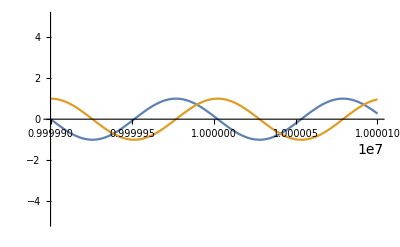

```mathematica
Plot[{Re[ψ[r]],Im[ψ[r]]},{r,rpos-100,rpos+100},PlotRange->5]
```

```mathematica
ReIm[ψ[r0]]
```

{5.03322425860284×10^480,-2.4667479701297×10^484}

## r_in

```mathematica
Clear[a,M,m,λ,ω,m,k,rp]
```

```mathematica
(*rp = M+√(M^2-a^2);*)
```

```mathematica
Δ[r_]:=r^2-2M r+a^2;
```

```mathematica
Win[r_]:=(((r^2+a^2)ω-a m)/r^2)^2-Δ[r]/r^4(λ-2a m ω+a^2 ω^2+(2(M r-a^2))/r^2)
```

```mathematica
hold=Simplify[Expand[((D[Exp[-ⅈ γ rs] c[k] (r[rs]-rp)^k,{rs,2}]+Win[r[rs]]Exp[-ⅈ γ rs] c[k] (r[rs]-rp)^k)==0/.{r[rs]->r,r'[rs]->Δ[r]/r^2,r''[rs]->D[Δ[r]/r^2,r] Δ[r]/r^2})],Assumptions->{ω>0,a>0,m>0,M>0,δ>0}]
```

1/r(r-rp)^(-1+k) (a^4 ((2-3 k+k^2) r^2+2 (-2+k) r rp+2 rp^2)-4 a m M r^3 (r-rp)^2 ω-r^2 (-k^2 r^4-4 M^2 ((-1+k)^2 r^2+(-2+k) r rp+rp^2)+k r^4 (1+2 ⅈ r γ-2 ⅈ rp γ)+2 M r (-2 ⅈ k r^3 γ+r^2 (1-3 k+2 k^2+2 ⅈ k rp γ-λ)-rp^2 (-1+λ)+r rp (-2+k+2 λ))+r^2 (r-rp)^2 (λ+r^2 (γ^2-ω^2)))+a^2 r (2 M (-3 (-2+k) r rp-3 rp^2+r^4 ω^2-2 r^3 rp ω^2+r^2 (-3+5 k-2 k^2+rp^2 ω^2))+r (rp^2 (2+m^2-λ)+2 r rp (-2+k-m^2+λ)+r^4 ω^2+r^3 (-2 ⅈ k γ-2 rp ω^2)+r^2 (2-4 k+2 k^2+m^2+2 ⅈ k rp γ-λ+rp^2 ω^2)))) c[k]==0

```mathematica
Expand[Simplify[hold[[1,2;;]],Assumptions->Placeholder]]
```

(r-rp)^(-1+k) (a^4 ((2-3 k+k^2) r^2+2 (-2+k) r rp+2 rp^2)-4 a m M r^3 (r-rp)^2 ω-r^2 (-k^2 r^4-4 M^2 ((-1+k)^2 r^2+(-2+k) r rp+rp^2)+k r^4 (1+2 ⅈ r γ-2 ⅈ rp γ)+2 M r (-2 ⅈ k r^3 γ+r^2 (1-3 k+2 k^2+2 ⅈ k rp γ-λ)-rp^2 (-1+λ)+r rp (-2+k+2 λ))+r^2 (r-rp)^2 (λ+r^2 (γ^2-ω^2)))+a^2 r (2 M (-3 (-2+k) r rp-3 rp^2+r^4 ω^2-2 r^3 rp ω^2+r^2 (-3+5 k-2 k^2+rp^2 ω^2))+r (rp^2 (2+m^2-λ)+2 r rp (-2+k-m^2+λ)+r^4 ω^2+r^3 (-2 ⅈ k γ-2 rp ω^2)+r^2 (2-4 k+2 k^2+m^2+2 ⅈ k rp γ-λ+rp^2 ω^2)))) c[k]

```mathematica
res = Expand[Simplify[ hold[[1,2]]c[k]]]
```

-a^4 k rp^2 c[k]+a^4 k^2 rp^2 c[k]+4 a^2 k M rp^3 c[k]-4 a^2 k^2 M rp^3 c[k]-2 a^2 k rp^4 c[k]+2 a^2 k^2 rp^4 c[k]-4 k M^2 rp^4 c[k]+4 k^2 M^2 rp^4 c[k]+4 k M rp^5 c[k]-4 k^2 M rp^5 c[k]-k rp^6 c[k]+k^2 rp^6 c[k]-4 a^4 k rp δ c[k]+2 a^4 k^2 rp δ c[k]+18 a^2 k M rp^2 δ c[k]-12 a^2 k^2 M rp^2 δ c[k]-10 a^2 k rp^3 δ c[k]+8 a^2 k^2 rp^3 δ c[k]-20 k M^2 rp^3 δ c[k]+16 k^2 M^2 rp^3 δ c[k]+22 k M rp^4 δ c[k]-20 k^2 M rp^4 δ c[k]-6 k rp^5 δ c[k]+6 k^2 rp^5 δ c[k]-2 ⅈ a^2 k rp^4 γ δ c[k]+4 ⅈ k M rp^5 γ δ c[k]-2 ⅈ k rp^6 γ δ c[k]+2 a^4 δ^2 c[k]-3 a^4 k δ^2 c[k]+a^4 k^2 δ^2 c[k]-6 a^2 M rp δ^2 c[k]+24 a^2 k M rp δ^2 c[k]-12 a^2 k^2 M rp δ^2 c[k]+2 a^2 rp^2 δ^2 c[k]-18 a^2 k rp^2 δ^2 c[k]+12 a^2 k^2 rp^2 δ^2 c[k]+a^2 m^2 rp^2 δ^2 c[k]+4 M^2 rp^2 δ^2 c[k]-36 k M^2 rp^2 δ^2 c[k]+24 k^2 M^2 rp^2 δ^2 c[k]-2 M rp^3 δ^2 c[k]+48 k M rp^3 δ^2 c[k]-40 k^2 M rp^3 δ^2 c[k]-15 k rp^4 δ^2 c[k]+15 k^2 rp^4 δ^2 c[k]-8 ⅈ a^2 k rp^3 γ δ^2 c[k]+20 ⅈ k M rp^4 γ δ^2 c[k]-12 ⅈ k rp^5 γ δ^2 c[k]-rp^6 γ^2 δ^2 c[k]-6 a^2 M δ^3 c[k]+10 a^2 k M δ^3 c[k]-4 a^2 k^2 M δ^3 c[k]+4 a^2 rp δ^3 c[k]-14 a^2 k rp δ^3 c[k]+8 a^2 k^2 rp δ^3 c[k]+2 a^2 m^2 rp δ^3 c[k]+8 M^2 rp δ^3 c[k]-28 k M^2 rp δ^3 c[k]+16 k^2 M^2 rp δ^3 c[k]-6 M rp^2 δ^3 c[k]+52 k M rp^2 δ^3 c[k]-40 k^2 M rp^2 δ^3 c[k]-20 k rp^3 δ^3 c[k]+20 k^2 rp^3 δ^3 c[k]-12 ⅈ a^2 k rp^2 γ δ^3 c[k]+40 ⅈ k M rp^3 γ δ^3 c[k]-30 ⅈ k rp^4 γ δ^3 c[k]-6 rp^5 γ^2 δ^3 c[k]+2 a^2 δ^4 c[k]-4 a^2 k δ^4 c[k]+2 a^2 k^2 δ^4 c[k]+a^2 m^2 δ^4 c[k]+4 M^2 δ^4 c[k]-8 k M^2 δ^4 c[k]+4 k^2 M^2 δ^4 c[k]-6 M rp δ^4 c[k]+28 k M rp δ^4 c[k]-20 k^2 M rp δ^4 c[k]-15 k rp^2 δ^4 c[k]+15 k^2 rp^2 δ^4 c[k]-8 ⅈ a^2 k rp γ δ^4 c[k]+40 ⅈ k M rp^2 γ δ^4 c[k]-40 ⅈ k rp^3 γ δ^4 c[k]-15 rp^4 γ^2 δ^4 c[k]-2 M δ^5 c[k]+6 k M δ^5 c[k]-4 k^2 M δ^5 c[k]-6 k rp δ^5 c[k]+6 k^2 rp δ^5 c[k]-2 ⅈ a^2 k γ δ^5 c[k]+20 ⅈ k M rp γ δ^5 c[k]-30 ⅈ k rp^2 γ δ^5 c[k]-20 rp^3 γ^2 δ^5 c[k]-k δ^6 c[k]+k^2 δ^6 c[k]+4 ⅈ k M γ δ^6 c[k]-12 ⅈ k rp γ δ^6 c[k]-15 rp^2 γ^2 δ^6 c[k]-2 ⅈ k γ δ^7 c[k]-6 rp γ^2 δ^7 c[k]-γ^2 δ^8 c[k]-a^2 rp^2 δ^2 λ c[k]+2 M rp^3 δ^2 λ c[k]-rp^4 δ^2 λ c[k]-2 a^2 rp δ^3 λ c[k]+6 M rp^2 δ^3 λ c[k]-4 rp^3 δ^3 λ c[k]-a^2 δ^4 λ c[k]+6 M rp δ^4 λ c[k]-6 rp^2 δ^4 λ c[k]+2 M δ^5 λ c[k]-4 rp δ^5 λ c[k]-δ^6 λ c[k]-4 a m M rp^3 δ^2 ω c[k]-12 a m M rp^2 δ^3 ω c[k]-12 a m M rp δ^4 ω c[k]-4 a m M δ^5 ω c[k]+2 a^2 M rp^3 δ^2 ω^2 c[k]+a^2 rp^4 δ^2 ω^2 c[k]+rp^6 δ^2 ω^2 c[k]+6 a^2 M rp^2 δ^3 ω^2 c[k]+4 a^2 rp^3 δ^3 ω^2 c[k]+6 rp^5 δ^3 ω^2 c[k]+6 a^2 M rp δ^4 ω^2 c[k]+6 a^2 rp^2 δ^4 ω^2 c[k]+15 rp^4 δ^4 ω^2 c[k]+2 a^2 M δ^5 ω^2 c[k]+4 a^2 rp δ^5 ω^2 c[k]+20 rp^3 δ^5 ω^2 c[k]+a^2 δ^6 ω^2 c[k]+15 rp^2 δ^6 ω^2 c[k]+6 rp δ^7 ω^2 c[k]+δ^8 ω^2 c[k]

```mathematica
Table[b[i]=Simplify[Coefficient[res,δ,i]],{i,-2,14}]
```

{0,0,(-1+k) k rp^2 (a^2+rp (-2 M+rp))^2 c[k],2 k rp (a^2+rp (-2 M+rp)) (a^2 (-2+k)+rp ((5-4 k) M+rp (-3+3 k-ⅈ rp γ))) c[k],(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2)))) c[k],-2 (6 a m M rp^2 ω+a^2 (M (3-5 k+2 k^2-3 rp^2 ω^2)+rp (-2-4 k^2-m^2+k (7+6 ⅈ rp γ)+λ-2 rp^2 ω^2))+rp (-2 (2-7 k+4 k^2) M^2+M rp (3+20 k^2+k (-26-20 ⅈ rp γ)-3 λ)+rp^2 (-10 k^2+5 k (2+3 ⅈ rp γ)+2 λ+3 rp^2 (γ^2-ω^2)))) c[k],(4 (-1+k)^2 M^2+2 M rp (-3+14 k-10 k^2+20 ⅈ k rp γ+3 λ)-12 a m M rp ω+a^2 (2+2 k^2+m^2+k (-4-8 ⅈ rp γ)-λ+6 M rp ω^2+6 rp^2 ω^2)-rp^2 (-15 k^2+5 k (3+8 ⅈ rp γ)+6 λ+15 rp^2 (γ^2-ω^2))) c[k],-2 (-3 k^2 rp+k (3 rp+ⅈ a^2 γ+15 ⅈ rp^2 γ)+M (1+2 k^2+k (-3-10 ⅈ rp γ)-λ+2 a m ω-a^2 ω^2)+2 rp (λ-a^2 ω^2+5 rp^2 (γ^2-ω^2))) c[k],(k^2+ⅈ k (ⅈ+4 M γ-12 rp γ)-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2)) c[k],2 (-ⅈ k γ+3 rp (-γ^2+ω^2)) c[k],(-γ^2+ω^2) c[k],0,0,0,0,0,0}

```mathematica
b[8]
```

(-γ^2+ω^2) c[k]

```mathematica
Together[(-γ^2+ω^2) c[k]]
```

-(γ^2-ω^2) c[k]

```mathematica
resIn=Collect[Solve[(Sum[b[i]/.k->k-i+2,{i,2,8}])==0,c[k]],c[_],Simplify][[1,1]]
```

c[k]→((γ^2-ω^2) c[-6+k])/(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))))+((2 ⅈ (-5+k) γ+6 rp γ^2-6 rp ω^2) c[-5+k])/(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))))+((-(-4+k)^2+(-4+k) (1-4 ⅈ M γ+12 ⅈ rp γ)+λ-a^2 ω^2+15 rp^2 (γ^2-ω^2)) c[-4+k])/(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))))+(2 (-3 (-3+k)^2 rp+(-3+k) (3 rp+ⅈ a^2 γ+15 ⅈ rp^2 γ)+M (1+2 (-3+k)^2+(-3+k) (-3-10 ⅈ rp γ)-λ+2 a m ω-a^2 ω^2)+2 rp (λ-a^2 ω^2+5 rp^2 (γ^2-ω^2))) c[-3+k])/(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))))+((-4 (-3+k)^2 M^2+2 M rp (71+10 k^2+40 ⅈ rp γ+k (-54-20 ⅈ rp γ)-3 λ)+12 a m M rp ω-a^2 (2+2 (-2+k)^2+m^2+(-2+k) (-4-8 ⅈ rp γ)-λ+6 M rp ω^2+6 rp^2 ω^2)+rp^2 (-15 (-2+k)^2+5 (-2+k) (3+8 ⅈ rp γ)+6 λ+15 rp^2 (γ^2-ω^2))) c[-2+k])/(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))))+(2 (6 a m M rp^2 ω+a^2 (M (10-9 k+2 k^2-3 rp^2 ω^2)+rp (-2-4 (-1+k)^2-m^2+(-1+k) (7+6 ⅈ rp γ)+λ-2 rp^2 ω^2))+rp (-2 (13-15 k+4 k^2) M^2+M rp (3+20 (-1+k)^2+(-1+k) (-26-20 ⅈ rp γ)-3 λ)+rp^2 (-10 (-1+k)^2+5 (-1+k) (2+3 ⅈ rp γ)+2 λ+3 rp^2 (γ^2-ω^2)))) c[-1+k])/(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))))

```mathematica
Simplify[{b[0],b[1],b[3],b[4]}/.rp->M+Sqrt[M^2-a^2]]
```

{0,0,-2 (-6 a^3 m M ω+12 a m M^2 (M+√(-a^2+M^2)) ω+2 M^2 (M+√(-a^2+M^2)) (1+k-4 k^2+20 ⅈ k M γ+λ+24 M^2 (γ^2-ω^2))+a^4 (9 ⅈ k γ+3 M (5 γ^2-2 ω^2)+√(-a^2+M^2) (3 γ^2-ω^2))-a^2 (√(-a^2+M^2) (2+3 k-6 k^2+m^2+λ)+M (2-8 k^2+m^2+k (2+28 ⅈ √(-a^2+M^2) γ)+2 λ)+M^3 (60 γ^2-46 ω^2)+M^2 (48 ⅈ k γ+2 √(-a^2+M^2) (18 γ^2-11 ω^2)))) c[k],(4 (-1+k)^2 M^2+2 M (M+√(-a^2+M^2)) (-3+14 k-10 k^2+20 ⅈ k (M+√(-a^2+M^2)) γ+3 λ)-12 a m M (M+√(-a^2+M^2)) ω+a^2 (2+2 k^2+m^2-4 ⅈ k (-ⅈ+2 M γ+2 √(-a^2+M^2) γ)-λ-6 a^2 ω^2+18 M^2 ω^2+18 M √(-a^2+M^2) ω^2)-(M+√(-a^2+M^2))^2 (-15 k^2+5 k (3+8 ⅈ (M+√(-a^2+M^2)) γ)+6 λ+15 (M+√(-a^2+M^2))^2 (γ^2-ω^2))) c[k]}

```mathematica
(*=0, so multiply by (rp+δ)^6*)
```

```mathematica
(temp = CoefficientList[r hold /.{r->δ+rp}//Expand,δ]//Simplify)//MatrixForm
```

(rp ((δ^(-1+k) (-a^4 (2 δ^2+k^2 (rp+δ)^2-k (rp^2+4 rp δ+3 δ^2))+4 a m M δ^2 (rp+δ)^3 ω-a^2 (rp+δ) (-2 k^2 (2 M-rp-δ) (rp+δ)^2+2 k (rp+δ) (M (2 rp+5 δ)-ⅈ (rp+δ) (rp (-ⅈ+γ δ)+δ (-2 ⅈ+γ δ)))+δ^2 (2 M (-3+rp^2 ω^2+2 rp δ ω^2+δ^2 ω^2)+(rp+δ) (2+m^2-λ+rp^2 ω^2+2 rp δ ω^2+δ^2 ω^2)))+(rp+δ)^2 (-k^2 (rp+δ)^2 (-2 M+rp+δ)^2+k (2 M-rp-δ) (rp+δ) (2 M (rp+2 δ)-ⅈ (rp+δ)^2 (-ⅈ+2 γ δ))+δ^2 (-4 M^2-2 M (rp+δ) (-1+λ)+(rp+δ)^2 (γ^2 δ^2+λ-δ^2 ω^2+rp^2 (γ^2-ω^2)+2 rp δ (γ^2-ω^2))))) c[k])/(rp+δ)==0)
(δ^(-1+k) (-a^4 (2 δ^2+k^2 (rp+δ)^2-k (rp^2+4 rp δ+3 δ^2))+4 a m M δ^2 (rp+δ)^3 ω-a^2 (rp+δ) (-2 k^2 (2 M-rp-δ) (rp+δ)^2+2 k (rp+δ) (M (2 rp+5 δ)-ⅈ (rp+δ) (rp (-ⅈ+γ δ)+δ (-2 ⅈ+γ δ)))+δ^2 (2 M (-3+rp^2 ω^2+2 rp δ ω^2+δ^2 ω^2)+(rp+δ) (2+m^2-λ+rp^2 ω^2+2 rp δ ω^2+δ^2 ω^2)))+(rp+δ)^2 (-k^2 (rp+δ)^2 (-2 M+rp+δ)^2+k (2 M-rp-δ) (rp+δ) (2 M (rp+2 δ)-ⅈ (rp+δ)^2 (-ⅈ+2 γ δ))+δ^2 (-4 M^2-2 M (rp+δ) (-1+λ)+(rp+δ)^2 (γ^2 δ^2+λ-δ^2 ω^2+rp^2 (γ^2-ω^2)+2 rp δ (γ^2-ω^2))))) c[k])/(rp+δ)==0)

```mathematica
hold[[1,2;;]]/.{r->δ+rp}//Expand
```

-a^4 k rp^2 δ^(-1+k) c[k]+a^4 k^2 rp^2 δ^(-1+k) c[k]+4 a^2 k M rp^3 δ^(-1+k) c[k]-4 a^2 k^2 M rp^3 δ^(-1+k) c[k]-2 a^2 k rp^4 δ^(-1+k) c[k]+2 a^2 k^2 rp^4 δ^(-1+k) c[k]-4 k M^2 rp^4 δ^(-1+k) c[k]+4 k^2 M^2 rp^4 δ^(-1+k) c[k]+4 k M rp^5 δ^(-1+k) c[k]-4 k^2 M rp^5 δ^(-1+k) c[k]-k rp^6 δ^(-1+k) c[k]+k^2 rp^6 δ^(-1+k) c[k]-4 a^4 k rp δ^k c[k]+2 a^4 k^2 rp δ^k c[k]+18 a^2 k M rp^2 δ^k c[k]-12 a^2 k^2 M rp^2 δ^k c[k]-10 a^2 k rp^3 δ^k c[k]+8 a^2 k^2 rp^3 δ^k c[k]-20 k M^2 rp^3 δ^k c[k]+16 k^2 M^2 rp^3 δ^k c[k]+22 k M rp^4 δ^k c[k]-20 k^2 M rp^4 δ^k c[k]-6 k rp^5 δ^k c[k]+6 k^2 rp^5 δ^k c[k]-2 ⅈ a^2 k rp^4 γ δ^k c[k]+4 ⅈ k M rp^5 γ δ^k c[k]-2 ⅈ k rp^6 γ δ^k c[k]+2 a^4 δ^(1+k) c[k]-3 a^4 k δ^(1+k) c[k]+a^4 k^2 δ^(1+k) c[k]-6 a^2 M rp δ^(1+k) c[k]+24 a^2 k M rp δ^(1+k) c[k]-12 a^2 k^2 M rp δ^(1+k) c[k]+2 a^2 rp^2 δ^(1+k) c[k]-18 a^2 k rp^2 δ^(1+k) c[k]+12 a^2 k^2 rp^2 δ^(1+k) c[k]+a^2 m^2 rp^2 δ^(1+k) c[k]+4 M^2 rp^2 δ^(1+k) c[k]-36 k M^2 rp^2 δ^(1+k) c[k]+24 k^2 M^2 rp^2 δ^(1+k) c[k]-2 M rp^3 δ^(1+k) c[k]+48 k M rp^3 δ^(1+k) c[k]-40 k^2 M rp^3 δ^(1+k) c[k]-15 k rp^4 δ^(1+k) c[k]+15 k^2 rp^4 δ^(1+k) c[k]-8 ⅈ a^2 k rp^3 γ δ^(1+k) c[k]+20 ⅈ k M rp^4 γ δ^(1+k) c[k]-12 ⅈ k rp^5 γ δ^(1+k) c[k]-rp^6 γ^2 δ^(1+k) c[k]-6 a^2 M δ^(2+k) c[k]+10 a^2 k M δ^(2+k) c[k]-4 a^2 k^2 M δ^(2+k) c[k]+4 a^2 rp δ^(2+k) c[k]-14 a^2 k rp δ^(2+k) c[k]+8 a^2 k^2 rp δ^(2+k) c[k]+2 a^2 m^2 rp δ^(2+k) c[k]+8 M^2 rp δ^(2+k) c[k]-28 k M^2 rp δ^(2+k) c[k]+16 k^2 M^2 rp δ^(2+k) c[k]-6 M rp^2 δ^(2+k) c[k]+52 k M rp^2 δ^(2+k) c[k]-40 k^2 M rp^2 δ^(2+k) c[k]-20 k rp^3 δ^(2+k) c[k]+20 k^2 rp^3 δ^(2+k) c[k]-12 ⅈ a^2 k rp^2 γ δ^(2+k) c[k]+40 ⅈ k M rp^3 γ δ^(2+k) c[k]-30 ⅈ k rp^4 γ δ^(2+k) c[k]-6 rp^5 γ^2 δ^(2+k) c[k]+2 a^2 δ^(3+k) c[k]-4 a^2 k δ^(3+k) c[k]+2 a^2 k^2 δ^(3+k) c[k]+a^2 m^2 δ^(3+k) c[k]+4 M^2 δ^(3+k) c[k]-8 k M^2 δ^(3+k) c[k]+4 k^2 M^2 δ^(3+k) c[k]-6 M rp δ^(3+k) c[k]+28 k M rp δ^(3+k) c[k]-20 k^2 M rp δ^(3+k) c[k]-15 k rp^2 δ^(3+k) c[k]+15 k^2 rp^2 δ^(3+k) c[k]-8 ⅈ a^2 k rp γ δ^(3+k) c[k]+40 ⅈ k M rp^2 γ δ^(3+k) c[k]-40 ⅈ k rp^3 γ δ^(3+k) c[k]-15 rp^4 γ^2 δ^(3+k) c[k]-2 M δ^(4+k) c[k]+6 k M δ^(4+k) c[k]-4 k^2 M δ^(4+k) c[k]-6 k rp δ^(4+k) c[k]+6 k^2 rp δ^(4+k) c[k]-2 ⅈ a^2 k γ δ^(4+k) c[k]+20 ⅈ k M rp γ δ^(4+k) c[k]-30 ⅈ k rp^2 γ δ^(4+k) c[k]-20 rp^3 γ^2 δ^(4+k) c[k]-k δ^(5+k) c[k]+k^2 δ^(5+k) c[k]+4 ⅈ k M γ δ^(5+k) c[k]-12 ⅈ k rp γ δ^(5+k) c[k]-15 rp^2 γ^2 δ^(5+k) c[k]-2 ⅈ k γ δ^(6+k) c[k]-6 rp γ^2 δ^(6+k) c[k]-γ^2 δ^(7+k) c[k]-a^2 rp^2 δ^(1+k) λ c[k]+2 M rp^3 δ^(1+k) λ c[k]-rp^4 δ^(1+k) λ c[k]-2 a^2 rp δ^(2+k) λ c[k]+6 M rp^2 δ^(2+k) λ c[k]-4 rp^3 δ^(2+k) λ c[k]-a^2 δ^(3+k) λ c[k]+6 M rp δ^(3+k) λ c[k]-6 rp^2 δ^(3+k) λ c[k]+2 M δ^(4+k) λ c[k]-4 rp δ^(4+k) λ c[k]-δ^(5+k) λ c[k]-4 a m M rp^3 δ^(1+k) ω c[k]-12 a m M rp^2 δ^(2+k) ω c[k]-12 a m M rp δ^(3+k) ω c[k]-4 a m M δ^(4+k) ω c[k]+2 a^2 M rp^3 δ^(1+k) ω^2 c[k]+a^2 rp^4 δ^(1+k) ω^2 c[k]+rp^6 δ^(1+k) ω^2 c[k]+6 a^2 M rp^2 δ^(2+k) ω^2 c[k]+4 a^2 rp^3 δ^(2+k) ω^2 c[k]+6 rp^5 δ^(2+k) ω^2 c[k]+6 a^2 M rp δ^(3+k) ω^2 c[k]+6 a^2 rp^2 δ^(3+k) ω^2 c[k]+15 rp^4 δ^(3+k) ω^2 c[k]+2 a^2 M δ^(4+k) ω^2 c[k]+4 a^2 rp δ^(4+k) ω^2 c[k]+20 rp^3 δ^(4+k) ω^2 c[k]+a^2 δ^(5+k) ω^2 c[k]+15 rp^2 δ^(5+k) ω^2 c[k]+6 rp δ^(6+k) ω^2 c[k]+δ^(7+k) ω^2 c[k]

```mathematica
temp[[2]]/.{k->n-1}//Simplify
```

2 (-1+n) rp (a^2+rp (-2 M+rp)) (a^2 (-3+n)+rp (M (9-4 n)+rp (-6+3 n-ⅈ rp γ)))

```mathematica
temp[[3]]/.{k->n-2}//Simplify
```

a^4 (12-7 n+n^2)-4 a m M rp^3 ω+a^2 rp (-2 M (51-36 n+6 n^2-rp^2 ω^2)+rp (2+m^2+12 (-2+n)^2+(-2+n) (-18-8 ⅈ rp γ)-λ+rp^2 ω^2))+rp^2 (4 M^2 (43-33 n+6 n^2)+2 M rp (-1-20 (-2+n)^2+2 (-2+n) (12+5 ⅈ rp γ)+λ)-rp^2 (-15 (-2+n)^2+3 (-2+n) (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2)))

```mathematica
temp[[4]]/.{k->n-3}
```

-2 (-3 (-3+n)^2 rp+(-3+n) (3 rp+ⅈ a^2 γ+15 ⅈ rp^2 γ)+M (1+2 (-3+n)^2+(-3+n) (-3-10 ⅈ rp γ)-λ+2 a m ω-a^2 ω^2)+2 rp (λ-a^2 ω^2+5 rp^2 (γ^2-ω^2)))

```mathematica
temp[[5]]/.{k->n-4}
```

(-4+n)^2+ⅈ (-4+n) (ⅈ+4 M γ-12 rp γ)-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2)

```mathematica
temp[[6]]/.{k->n-5}
```

-2 ⅈ (-5+n) γ+6 rp (-γ^2+ω^2)

```mathematica
temp[[7]]
```

-γ^2+ω^2

```mathematica
Length[temp]
```

7

```mathematica
ψ [rs_]:= Exp[-ⅈ γ rs]ck(r[rs]-rp)^k
```

```mathematica
D[ψ[rs],{rs,2}]//Simplify
```

-ck ⅇ^(-ⅈ rs γ) (-rp+r[rs])^(-2+k) (γ^2 r[rs]^2-2 ⅈ k rp γ r'[rs]-(-1+k) k r'[rs]^2+rp (rp γ^2+k r''[rs])-r[rs] (2 rp γ^2-2 ⅈ k γ r'[rs]+k r''[rs]))

```mathematica
a^4 (2 δ^2+k^2 (rp+δ)^2-k (rp^2+4 rp δ+3 δ^2))-4 a m M δ^2 (rp+δ)^3 ω+a^2 (rp+δ) (-2 k^2 (2 M-rp-δ) (rp+δ)^2+2 k (rp+δ) (M (2 rp+5 δ)-ⅈ (rp+δ) (rp (-ⅈ+γ δ)+δ (-2 ⅈ+γ δ)))+δ^2 (2 M (-3+rp^2 ω^2+2 rp δ ω^2+δ^2 ω^2)+(rp+δ) (2+m^2-λ+rp^2 ω^2+2 rp δ ω^2+δ^2 ω^2)))-(rp+δ)^2 (-k^2 (rp+δ)^2 (-2 M+rp+δ)^2+k (2 M-rp-δ) (rp+δ) (2 M (rp+2 δ)-ⅈ (rp+δ)^2 (-ⅈ+2 γ δ))+δ^2 (-4 M^2-2 M (rp+δ) (-1+λ)+(rp+δ)^2 (γ^2 δ^2+λ-δ^2 ω^2+rp^2 (γ^2-ω^2)+2 rp δ (γ^2-ω^2))))//Expand
```

-a^4 k rp^2+a^4 k^2 rp^2+4 a^2 k M rp^3-4 a^2 k^2 M rp^3-2 a^2 k rp^4+2 a^2 k^2 rp^4-4 k M^2 rp^4+4 k^2 M^2 rp^4+4 k M rp^5-4 k^2 M rp^5-k rp^6+k^2 rp^6-4 a^4 k rp δ+2 a^4 k^2 rp δ+18 a^2 k M rp^2 δ-12 a^2 k^2 M rp^2 δ-10 a^2 k rp^3 δ+8 a^2 k^2 rp^3 δ-20 k M^2 rp^3 δ+16 k^2 M^2 rp^3 δ+22 k M rp^4 δ-20 k^2 M rp^4 δ-6 k rp^5 δ+6 k^2 rp^5 δ-2 ⅈ a^2 k rp^4 γ δ+4 ⅈ k M rp^5 γ δ-2 ⅈ k rp^6 γ δ+2 a^4 δ^2-3 a^4 k δ^2+a^4 k^2 δ^2-6 a^2 M rp δ^2+24 a^2 k M rp δ^2-12 a^2 k^2 M rp δ^2+2 a^2 rp^2 δ^2-18 a^2 k rp^2 δ^2+12 a^2 k^2 rp^2 δ^2+a^2 m^2 rp^2 δ^2+4 M^2 rp^2 δ^2-36 k M^2 rp^2 δ^2+24 k^2 M^2 rp^2 δ^2-2 M rp^3 δ^2+48 k M rp^3 δ^2-40 k^2 M rp^3 δ^2-15 k rp^4 δ^2+15 k^2 rp^4 δ^2-8 ⅈ a^2 k rp^3 γ δ^2+20 ⅈ k M rp^4 γ δ^2-12 ⅈ k rp^5 γ δ^2-rp^6 γ^2 δ^2-6 a^2 M δ^3+10 a^2 k M δ^3-4 a^2 k^2 M δ^3+4 a^2 rp δ^3-14 a^2 k rp δ^3+8 a^2 k^2 rp δ^3+2 a^2 m^2 rp δ^3+8 M^2 rp δ^3-28 k M^2 rp δ^3+16 k^2 M^2 rp δ^3-6 M rp^2 δ^3+52 k M rp^2 δ^3-40 k^2 M rp^2 δ^3-20 k rp^3 δ^3+20 k^2 rp^3 δ^3-12 ⅈ a^2 k rp^2 γ δ^3+40 ⅈ k M rp^3 γ δ^3-30 ⅈ k rp^4 γ δ^3-6 rp^5 γ^2 δ^3+2 a^2 δ^4-4 a^2 k δ^4+2 a^2 k^2 δ^4+a^2 m^2 δ^4+4 M^2 δ^4-8 k M^2 δ^4+4 k^2 M^2 δ^4-6 M rp δ^4+28 k M rp δ^4-20 k^2 M rp δ^4-15 k rp^2 δ^4+15 k^2 rp^2 δ^4-8 ⅈ a^2 k rp γ δ^4+40 ⅈ k M rp^2 γ δ^4-40 ⅈ k rp^3 γ δ^4-15 rp^4 γ^2 δ^4-2 M δ^5+6 k M δ^5-4 k^2 M δ^5-6 k rp δ^5+6 k^2 rp δ^5-2 ⅈ a^2 k γ δ^5+20 ⅈ k M rp γ δ^5-30 ⅈ k rp^2 γ δ^5-20 rp^3 γ^2 δ^5-k δ^6+k^2 δ^6+4 ⅈ k M γ δ^6-12 ⅈ k rp γ δ^6-15 rp^2 γ^2 δ^6-2 ⅈ k γ δ^7-6 rp γ^2 δ^7-γ^2 δ^8-a^2 rp^2 δ^2 λ+2 M rp^3 δ^2 λ-rp^4 δ^2 λ-2 a^2 rp δ^3 λ+6 M rp^2 δ^3 λ-4 rp^3 δ^3 λ-a^2 δ^4 λ+6 M rp δ^4 λ-6 rp^2 δ^4 λ+2 M δ^5 λ-4 rp δ^5 λ-δ^6 λ-4 a m M rp^3 δ^2 ω-12 a m M rp^2 δ^3 ω-12 a m M rp δ^4 ω-4 a m M δ^5 ω+2 a^2 M rp^3 δ^2 ω^2+a^2 rp^4 δ^2 ω^2+rp^6 δ^2 ω^2+6 a^2 M rp^2 δ^3 ω^2+4 a^2 rp^3 δ^3 ω^2+6 rp^5 δ^3 ω^2+6 a^2 M rp δ^4 ω^2+6 a^2 rp^2 δ^4 ω^2+15 rp^4 δ^4 ω^2+2 a^2 M δ^5 ω^2+4 a^2 rp δ^5 ω^2+20 rp^3 δ^5 ω^2+a^2 δ^6 ω^2+15 rp^2 δ^6 ω^2+6 rp δ^7 ω^2+δ^8 ω^2

```mathematica
Coefficient[c[k]/.resIn,c[k]]
```

0